## Pseudo-entropy under Joining Local Quenches in 4-Qubit Systems

```mathematica
(* Analyitical Results for two-level system, that is only two of the lambdas are non-ZERO*)
```

```mathematica
SE = - (lam0 Log[lam0]+lam1 Log[lam1]);
CE = (lam0 (Log[lam0])^2+lam1 (Log[lam1])^2)-SE^2;
phi0R = lam0 lam0^(I s) + lam1 lam1^(I s);
phi1R = 1/b1(lam0 (-Log[lam0]-SE)lam0^(I s)+ lam1(-Log[lam1]-SE)lam1^(I s));
b1 = Sqrt[lam0 (-Log[lam0]-SE)^2+lam1(-Log[lam1]-SE)^2];
phi0L = Conjugate[lam0] Conjugate[lam0]^(I s) + Conjugate[lam1] Conjugate[lam1]^(I s);
phi1L = 1/c1s(Conjugate[lam0] (-Log[Conjugate[lam0]]-Conjugate[SE])Conjugate[lam0]^(I s)+ Conjugate[lam1](-Log[Conjugate[lam1]]-Conjugate[SE])Conjugate[lam1]^(I s));
c1s = Sqrt[Conjugate[lam0] (-Log[Conjugate[lam0]]-Conjugate[SE])^2+Conjugate[lam1](-Log[Conjugate[lam1]]-Conjugate[SE])^2];
CompR = Abs[phi1R]^2/(Abs[phi0R]^2+Abs[phi1R]^2);
CompL = Abs[phi1L]^2/(Abs[phi0L]^2+Abs[phi1L]^2);
```

```mathematica
giveSEandCE[lamList_]:=(
SElam = Total[Table[-lam Log[lam],{lam,lamList}]];
CElam = Total[Table[lam Log[lam]^2,{lam,lamList}]]-SElam^2;
Return[{SElam,CElam}]
)
```

```mathematica
{SEpsi,CEpsi}= giveSEandCE[{Cos[thetap]^4,Sin[thetap]^4,Sin[thetap]^2 Cos[thetap]^2,Sin[thetap]^2 Cos[thetap]^2}];
{SEphi,CEphi} = giveSEandCE[{Cos[theta]^2,Sin[theta]^2}];
{SEpsiphi,CEpsiphi}=giveSEandCE[{(Cos[thetap]^2 Cos[theta])/(Cos[thetap]^2 Cos[theta]+Sin[thetap]^2 Sin[theta]Exp[-I phi]),(Sin[thetap]^2 Sin[theta]Exp[-I phi])/(Cos[thetap]^2 Cos[theta]+Sin[thetap]^2 Sin[theta]Exp[-I phi])}];
```

```mathematica
Show[DensityPlot[(SEpsiphi-(SEphi+SEpsi)/2)/.phi->0,{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->8],Frame->True,FrameLabel->{Style["θ",Black,22],Style["θ'",Black,22]},FrameTicks->{{{0,Pi/4,Pi/2},None},{{0,Pi/4,Pi/2},None}},FrameTicksStyle->Directive[Black,20]]
```

-Graphics-

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_0_DeltaSE.pdf",%78,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_0_DeltaSE.pdf

```mathematica
DensityPlot[SEpsiphi/.phi->0,{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"Rainbow",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->10]
```

-Graphics-

```mathematica
DensityPlot[(CEpsiphi-(CEphi+CEpsi)/2)/.phi->0,{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->8,Frame->True,FrameLabel->{Style["θ",Black,22],Style["θ'",Black,22]},FrameTicks->{{{0,Pi/4,Pi/2},None},{{0,Pi/4,Pi/2},None}},FrameTicksStyle->Directive[Black,20]]
```

-Graphics-

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_0_DeltaCE.pdf",%80,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_0_DeltaCE.pdf

```mathematica
DensityPlot[CEpsiphi/.phi->0,{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->10]
```

$Aborted

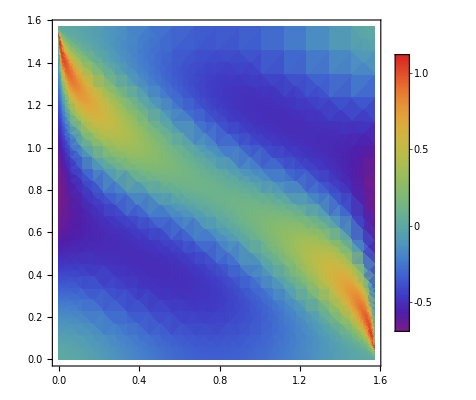

```mathematica
DensityPlot[Re[(SEpsiphi-(SEphi+SEpsi)/2)/.phi->Pi/2],{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"Rainbow",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->6]
```

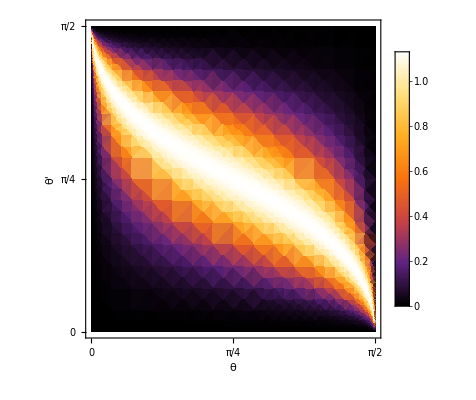

```mathematica
DensityPlot[Re[(SEpsiphi)/.phi->Pi/2],{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->6,Frame->True,FrameLabel->{Style["θ",Black,22],Style["θ'",Black,22]},FrameTicks->{{{0,Pi/4,Pi/2},None},{{0,Pi/4,Pi/2},None}},FrameTicksStyle->Directive[Black,20]]
```

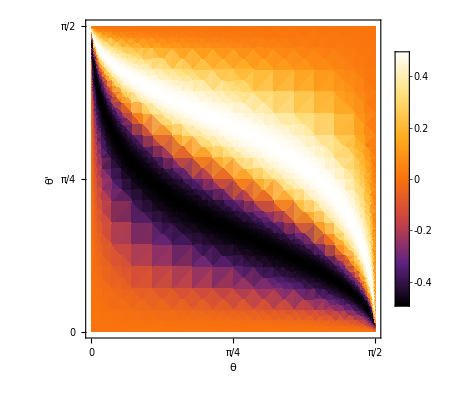

```mathematica
DensityPlot[Im[(SEpsiphi)/.phi->Pi/2],{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->6,Frame->True,FrameLabel->{Style["θ",Black,22],Style["θ'",Black,22]},FrameTicks->{{{0,Pi/4,Pi/2},None},{{0,Pi/4,Pi/2},None}},FrameTicksStyle->Directive[Black,20]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ReSE.pdf",%43,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ReSE.pdf

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ImSE.pdf",%53,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ImSE.pdf

```mathematica
DensityPlot[Re[(CEpsiphi-(CEphi+CEpsi)/2)/.phi->Pi/2],{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"Rainbow",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->6]
```

-Graphics-

```mathematica
DensityPlot[Re[(CEpsiphi)/.phi->Pi/2],{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->6,Frame->True,FrameLabel->{Style["θ",Black,22],Style["θ'",Black,22]},FrameTicks->{{{0,Pi/4,Pi/2},None},{{0,Pi/4,Pi/2},None}},FrameTicksStyle->Directive[Black,20]]
```

-Graphics-

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ReCE.pdf",%47,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ReCE.pdf

```mathematica
DensityPlot[Im[(CEpsiphi)/.phi->Pi/2],{theta,0,Pi/2},{thetap,0,Pi/2},ColorFunction->"SunsetColors",PlotLegends->Automatic,LabelStyle->Directive[Bold, Black,16],MaxRecursion->6,Frame->True,FrameLabel->{Style["θ",Black,22],Style["θ'",Black,22]},FrameTicks->{{{0,Pi/4,Pi/2},None},{{0,Pi/4,Pi/2},None}},FrameTicksStyle->Directive[Black,20]]
```

-Graphics-

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ImCE.pdf",%57,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_ImCE.pdf

## pseudoModular Complexity with θ=θ’ and ϕ=π/2

```mathematica
compRq = (CompR/.{lam0->(Cos[thetap]^2 Cos[theta])/(Cos[thetap]^2 Cos[theta]+Sin[thetap]^2 Sin[theta]Exp[-I phi]),lam1->(Sin[thetap]^2 Sin[theta]Exp[-I phi])/(Cos[thetap]^2 Cos[theta]+Sin[thetap]^2 Sin[theta]Exp[-I phi])})/.{thetap->theta};
compLq = (CompL/.{lam0->(Cos[thetap]^2 Cos[theta])/(Cos[thetap]^2 Cos[theta]+Sin[thetap]^2 Sin[theta]Exp[-I phi]),lam1->(Sin[thetap]^2 Sin[theta]Exp[-I phi])/(Cos[thetap]^2 Cos[theta]+Sin[thetap]^2 Sin[theta]Exp[-I phi])})/.{thetap->theta};
```

```mathematica
(* θ = 0*)
```

```mathematica
Plot[{compRq/.{theta->0.001,phi->Pi/2},compLq/.{theta->0.001,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red}]
```

-Graphics-

```mathematica
(*θ=Pi/10*)
```

```mathematica
Plot[{compRq/.{theta->Pi/10,phi->Pi/2},compLq/.{theta->Pi/10,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red}]
```

-Graphics-

```mathematica
(*θ=Pi/8*)
```

```mathematica
Plot[{compRq/.{theta->Pi/8,phi->Pi/2},compLq/.{theta->Pi/8,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red}]
```

-Graphics-

```mathematica
(*θ=(Pi/8+Pi/4)/2*)
```

```mathematica
Plot[{compRq/.{theta->(Pi/8+Pi/4)/2,phi->Pi/2},compLq/.{theta->(Pi/8+Pi/4)/2,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red}]
```

-Graphics-

```mathematica
(*θ=(Pi/8+2 Pi/4)/3*)
```

```mathematica
Plot[{compRq/.{theta->(Pi/8+2 Pi/4)/3,phi->Pi/2},compLq/.{theta->(Pi/8+2 Pi/4)/3,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red}]
```

-Graphics-

```mathematica
(*θ=(Pi/8+3 Pi/4)/4*)
```

```mathematica
Plot[{compRq/.{theta->(Pi/8+3 Pi/4)/4,phi->Pi/2},compLq/.{theta->(Pi/8+3 Pi/4)/4,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red}]
```

-Graphics-

```mathematica
(*θ=Pi/4*)
```

```mathematica
Plot[{compRq/.{theta->Pi/4,phi->Pi/2},compLq/.{theta->Pi/4,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red},PlotRange->All]
```

-Graphics-

```mathematica
(*θ=3Pi/8*)
```

```mathematica
Plot[{compRq/.{theta->3Pi/8,phi->Pi/2},compLq/.{theta->3Pi/8,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red},PlotRange->All]
```

-Graphics-

```mathematica
(*θ=Pi/2*)
```

```mathematica
Plot[{compRq/.{theta->Pi/2-0.001,phi->Pi/2},compLq/.{theta->Pi/2-0.001,phi->Pi/2}},{s,0,20},PlotStyle->{Blue,Red},PlotRange->All]
```

-Graphics-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
Plot[{compRq/.{theta->Pi/8,phi->Pi/2},compRq/.{theta->(Pi/8+Pi/4)/2,phi->Pi/2},compRq/.{theta->(Pi/8+2Pi/4)/3,phi->Pi/2},compRq/.{theta->(Pi/8+3Pi/4)/4,phi->Pi/2},compRq/.{theta->Pi/4-0.01,phi->Pi/2},compLq/.{theta->Pi/8,phi->Pi/2},compLq/.{theta->(Pi/8+Pi/4)/2,phi->Pi/2},compLq/.{theta->(Pi/8+2Pi/4)/3,phi->Pi/2},compLq/.{theta->(Pi/8+3Pi/4)/4,phi->Pi/2},compLq/.{theta->Pi/4-0.01,phi->Pi/2}},{s,0,6.5},PlotStyle->{RGBColor[0,0,1,0.2],RGBColor[0,0,1,0.4],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.75],RGBColor[0,0,1,1],RGBColor[1,0,0,0.2],RGBColor[1,0,0,0.4],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,0,1]},PlotRange->All,Frame->True,LabelStyle->Directive[Medium,Black,20],FrameLabel->{Style["s",Black,25],Style["C(s)",Black,25]}]
```

-Graphics-

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_Comp_full.pdf",%99,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_Comp_full.pdf

```mathematica
Plot[{compRq/.{theta->Pi/8,phi->Pi/2},compRq/.{theta->(Pi/8+Pi/4)/2,phi->Pi/2},compRq/.{theta->(Pi/8+2Pi/4)/3,phi->Pi/2},compRq/.{theta->(Pi/8+3Pi/4)/4,phi->Pi/2},compRq/.{theta->Pi/4-0.01,phi->Pi/2},compLq/.{theta->Pi/8,phi->Pi/2},compLq/.{theta->(Pi/8+Pi/4)/2,phi->Pi/2},compLq/.{theta->(Pi/8+2Pi/4)/3,phi->Pi/2},compLq/.{theta->(Pi/8+3Pi/4)/4,phi->Pi/2},compLq/.{theta->Pi/4-0.01,phi->Pi/2}},{s,0,0.5},PlotStyle->{RGBColor[0,0,1,0.2],RGBColor[0,0,1,0.4],RGBColor[0,0,1,0.55],RGBColor[0,0,1,0.75],RGBColor[0,0,1,1],RGBColor[1,0,0,0.2],RGBColor[1,0,0,0.4],RGBColor[1,0,0,0.55],RGBColor[1,0,0,0.75],RGBColor[1,0,0,1]},PlotRange->All,Frame->True,LabelStyle->Directive[Medium,Black,20],FrameLabel->{Style["s",Black,25],Style["C(s)",Black,25]}]
```

-Graphics-

```mathematica
Export["/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_Comp_early.pdf",%100,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/4qubit_phi_piby2_Comp_early.pdf